## Import data

```mathematica
plotFolder = "plots";

SetDirectory[NotebookDirectory[]];
data = {Import["points15_025.mx"], Import["points15_05.mx"], Import["points15_1.mx"], Import["points15_2.mx"]};
data[[1]];
```

## Import bounds data

```mathematica
bicep2021sigma1 = Import["BICEP_2021_sigma1.dat"];
bicep2021sigma2 = Import["BICEP_2021_sigma2.dat"];
bounds = {bicep2021sigma1, bicep2021sigma2};
boundsX = 3;
boundsY = 2;
boundsI = {boundsX, boundsY};
errorIndex = 6;
```

## Plot making functions

```mathematica
plotPoints[xindex_, yindex_, data_, plotlimits_, colour_] := Module[
{xdata, ydata},
xdata = Map[#[[xindex]]&, data];
ydata = Map[#[[yindex]]&, data];
ListPlot[Transpose[{xdata, ydata}], PlotStyle->colour, PlotRange->plotlimits]
];
plotArea[data_, colour_, limits_, fillOpacity_, lineOpacity_] := ListPlot[data,PlotRange-> limits,
LabelStyle-> FontSize-> 10,Joined-> True,PlotStyle->Opacity[lineOpacity,ColorData["Legacy"][colour]] ,Filling-> Axis,FillingStyle->Opacity[fillOpacity,ColorData["Legacy"][colour]]] ;

plotBounds[boundsdata_, colour_, limits_] :=plotArea[boundsdata, colour, limits, 0.25, 0.75]; 
plotCalculations[data_, colour_, limits_] := plotArea[data, colour, limits, 0.5, 0.5]
```

## Data transformations

```mathematica
getData[xindex_, yindex_, normalData_, reverseData_, limits_] := Module[{normalX, normalY, reverseX, reverseY, normalT, reverseT, allData, filtered},
normalX =  Map[#[[xindex]]&, normalData];
normalY = Map[#[[yindex]]&, normalData];
reverseX =  Map[#[[xindex]]&, reverseData];
reverseY = Map[#[[yindex]]&, reverseData];
normalT = Transpose[{normalX, normalY}];
reverseT = Reverse[Transpose[{reverseX, reverseY}]];
allData = Join[normalT, reverseT];
filtered = Select[allData, #[[1]]≥limits[[1, 1]]&&#[[1]]≤limits[[1,2]]&&#[[2]]≥limits[[2,1]]&&#[[2]]≤limits[[2,2]]&];
Append[filtered, filtered[[1]]]
]
getErrorPoints[xindex_, yindex_, normalData_, reverseData_, limits_] := Module[{normalX, normalY, normalErrors,  reverseX, reverseY, reverseErrors, normalT, reverseT, allData, errors, filtered},
normalX =  Map[#[[xindex]]&, normalData];
normalY = Map[#[[yindex]]&, normalData];
normalErrors = Map[#[[errorIndex]] &, normalData];
reverseX =  Map[#[[xindex]]&, reverseData];
reverseY = Map[#[[yindex]]&, reverseData];
reverseErrors = Map[#[[errorIndex]] &, reverseData];
normalT = Transpose[{normalX, normalY, normalErrors}];
reverseT = Reverse[Transpose[{reverseX, reverseY, reverseErrors}]];
allData = Join[normalT, reverseT];
errors = Select[allData, #[[3]] == 0 &];
filtered = Select[errors, #[[1]]≥limits[[1, 1]]&&#[[1]]≤limits[[1,2]]&&#[[2]]≥limits[[2,1]]&&#[[2]]≤limits[[2,2]] &];
Map[{#[[1]], #[[2]]} &, filtered]
]
PermutePoints[points_] := Module[{x1, x2, y1, y2},
x1 = points[[1, 1]];
x2 = points[[1, 2]];
y1 = points[[2, 1]];
y2 = points[[2, 2]];
{{x1, y1}, {x1, y2}, {x2, y2}, {x2, y1}, {x1, y1}}
]
```

## Bound plot logic

```mathematica
getNormalBoundPlots[bounds_, limits_, reverse_]:= Module[{lines1, lines2},
(*TODO: switch x and y if reverse is True*)
lines1 = plotBounds[bounds[[1]], "Gray", limits];
lines2 = plotBounds[bounds[[2]], "Gray", limits];
{lines1, lines2}
]
getSingleAxisBounds[bounds_, limits_, xindex_, yindex_] := Module[{indexFromBounds, boundsData, boundMinMax, limitIsX, limitData, lines1, lines2, points1, points2}, 
indexFromBounds = If[MemberQ[{xindex, yindex}, boundsX],1, 2];
boundsData = Map[#[[indexFromBounds]]&,bounds, {2}];
boundMinMax = Map[{Min[#], Max[#]}&, boundsData];
limitIsX = MemberQ[boundsI, yindex];
limitData = If[limitIsX, limits[[1]], limits[[2]]];
points1 = {limitData, boundMinMax[[1]]};
points2 = {limitData, boundMinMax[[2]]};
lines1 = plotBounds[PermutePoints[If[limitIsX, points1, Reverse[points1]]], "Gray", limits];
lines2 = plotBounds[PermutePoints[If[limitIsX, points2, Reverse[points2]]], "Gray", limits];
{lines1, lines2}
]
findBoundPlots[bounds_, limits_, xindex_, yindex_] := Module[{},
If[
!MemberQ[boundsI, xindex] && !MemberQ[boundsI, yindex], {}, 
If[
MemberQ[boundsI, xindex] && MemberQ[boundsI, yindex],
getNormalBoundPlots[bounds, limits, xindex==boundsY],
getSingleAxisBounds[bounds, limits, xindex, yindex]
]]
]
```

## Result plot logic

```mathematica
findResultPlots[xindex_, yindex_, data_, limits_] := Module[{data1, data2, data3, data4, lines1, lines2, lines3, lines4},
data1 = getData[xindex, yindex, data[[1]][[1]], data[[1]][[2]], limits];
data2 = getData[xindex, yindex, data[[2]][[1]], data[[2]][[2]], limits];
data3 = getData[xindex, yindex, data[[3]][[1]], data[[3]][[2]], limits];
data4 = getData[xindex, yindex, data[[4]][[1]], data[[4]][[2]], limits];
lines1 = plotCalculations[data1, "Purple", limits];
lines2 = plotCalculations[data2, "Cyan", limits];
lines3 = plotCalculations[data3, "Green", limits];
lines4 = plotCalculations[data4, "Blue", limits];
{lines1,  lines2, lines3, lines4}
]
```

## Find invalid points

```mathematica
findErrorPoints[xindex_, yindex_, data_, limits_] := Module[{blueData},
blueData = getErrorPoints[xindex, yindex, data[[1]], data[[2]], limits];
{ListPlot[Join[blueData], PlotStyle -> PointSize[Large]]}
];
```

## Plot function

```mathematica
(*Module takes 2 arguments, first is a list of variables that are bound to local scope, so even if there are global variables with the same name, they are not overwritten.
Second is the function itself*)
plotAllPoints[xindex_, yindex_, data_, limits_, labels_, bounds_] := Module[{resultPlots, boundPlots},
resultPlots = findResultPlots[xindex, yindex, data, limits];
boundPlots = findBoundPlots[bounds, limits, xindex, yindex];
(*errorPlots = findErrorPoints[xindex, yindex, data, limits];*)
Show[Join[boundPlots, resultPlots], AxesLabel->{Style[labels[[xindex]],Bold,13],Style[labels[[yindex]],Bold,13]}]
];
```

## Bounds

```mathematica
nsmin=0.94; (*0.93*)
nsmax=0.985; (*1*)
rmin=0;
rmax=0.2; (*0.4*)
δmin = 1.5;
δmax = 100;
λmin = 0;
λmax = 6*10^-14;

axeslabels = {"ϕ0", "r", "n_s", "λ", "δ"};
```

## r vs n_s

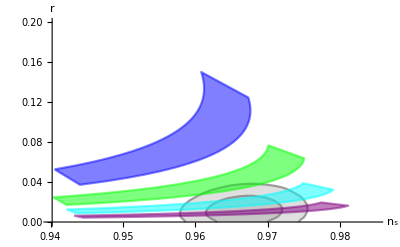

```mathematica
limits = {{nsmin, nsmax}, {rmin, rmax}};
plotAllPoints[3, 2, data, limits, axeslabels, bounds] 
Export[plotFolder <> "/r_vs_ns_15.pdf", %];
```

## r vs δ

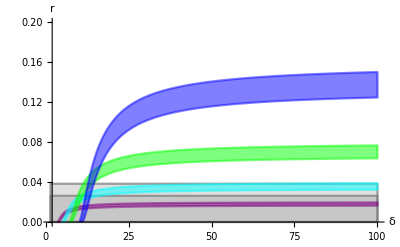

```mathematica
limits = {{δmin, δmax}, {rmin, rmax}};
plotAllPoints[5, 2, data, limits, axeslabels, bounds]
Export[plotFolder <> "/r_vs_delta_15.pdf", %];
```

## δ vs n_s

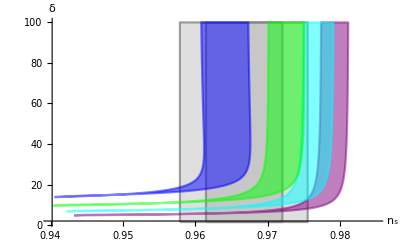

```mathematica
limits = {{nsmin, nsmax}, {δmin, δmax}};
plotAllPoints[3, 5, data, limits, axeslabels, bounds]
Export[plotFolder <> "/delta_vs_ns_15.pdf", %];
```

## λ vs δ

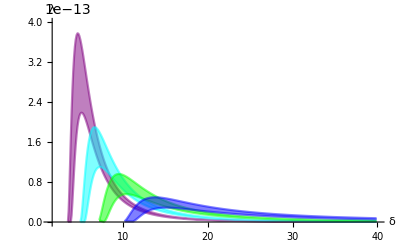

```mathematica
limits = {{δmin, 40}, {λmin,4*10^-13}};
plotAllPoints[5, 4, data, limits, axeslabels, bounds]
Export[plotFolder <> "/lambda_vs_delta_15.pdf", %];
```